## Verjetnost

1. Kupili smo 9 različnih knjig. Na koliko načinov jih lahko razporedimo na polici?
Rezultat: 9! = 362880.

```mathematica
n=9*8*7*6*5*4*3*2*1
n=9!
n=Factorial[9]
```

2. Janez ima 5 različnih knjig za matematiko, 4 različne knjige za fiziko in 6 različnih knjig za računalništvo.
	a) Na koliko načinov jih lahko razporedi na polici pri poljubni razporeditvi?
	b) Na koliko načinov jih lahko razporedi na polici, če naj bodo knjige iste stroke postavljene skupaj?
Rezultati: a) 15! = 1307674368000, b) 3!*5!*4!*6! = 12441600.

```mathematica
n1 = 15!
(* n2 = 
		3! - kombinacija strok: M-F-R, F-R-M,
		 5! - komvinacija znotraj matematike
	   4! - kombinacija fizike
	   6! - kombinacije računalništvo itd*)
```

3. Maja v slaščičarni, kjer imajo 8 vrst sladoleda, med drugim tudi okus čokolade, naroči porcijo s 3 različnimi kepicami sladoleda. 
	a) Na koliko načinov lahko izbere porcijo pri poljubnem izboru?
	b) Na koliko načinov lahko izbere porcijo, če zagotovoo izbere eno čokoladno kepico?
   Vrstni red izbire kepic ni pomemben.
Rezultati: a) 56, b) 21.

```mathematica
(* a primer *)
Binomial[8,3]
(* b primer *)
Binomial[7,2] (* ena je že izbrana,  preostalo se še lahko izbira *)
```

56

4. Iz števk od 1 do 9 sestavljamo petmestna števila brez ponavljanja števk. 
	a) Na koliko načinov lahko sestavimo števila pri poljubnem izboru?
	b) Na koliko načinov lahko sestavimo števila, če je ena izmed števk zagotovo 3?
	c) Na koliko načinov lahko sestavimo števila, če se število konča s števko 7?
Rezultati: a) 15120, b) 8400, c) 1680.

```mathematica
(* a primer *)
Binomial[9,5]*5! (*variacija -- vse kombinacije na 5 mest postavitve *)
9!/4!
(* b primer *)
Binomial[8,4]*5!
8!/4!*5
(* c primer *)
Binomial[8,4]*4!
8!/4!
```

15120

15120

8400

8400

1680

1680

5. Iz kupa 32 igralnih kart (7-10, fant, dama, kralj, as; križ, pik, srce, karo) na slepo potegnemo eno karto. 
	a) Izračunajte verjetnost, da je izvlečena karta dama.
	b) Izračunajte verjetnost, da je izvlečena karta karo ali desetka.
	c) Izračunajte verjetnost, da je izvlečena karta srčev kralj.
Rezultati: a) 1/8, b) 11/32, c) 1/32.

```mathematica
(* število ugodnih izidov / št vseh izidov *)
(* a primer *)
1/32
(* b primer *)
11/32
(* c primer *)
1/32
```

6. Iz števk od 2 do 6 sestavljamo petmestna števila brez ponavljanja števk. 
	a) Kolikšna je verjetnost, da bomo na slepo sestavili število 23456?
	b) Kolikšna je verjetnost, da bo na slepo sestavljeno število deljivo s 5?
Rezultati: a) 1/120, b) 1/5.

```mathematica
(* a primer *)
1/5!
(* b primer *)
(* na zadnjem mestu je fiksirana 5ka, potem ostanejo še 4 mesta *)
4!/5!
```

1/120

1/5

1/20

Seznam uporabljenih ukazov za delo s seznami v programu Mathematica:
Table[ ]
Range[ ]
CharacterRange[ ]
Sum[ ]
Length[ ]
Total[ ]
Count[ ]
First[ ]
Last[ ]
Take[ ]
Drop[ ]
Select[ ]
MemberQ[ ]
Join[ ]
Append[ ]
Prepend[ ]

Seznam uporabljenih ukazov za zaokroževanje, ostanek pri deljenju in delo s števili v programu Mathematica:
Floor[ ]
Ceiling[ ]
Round[ ]
Mod[ ]
IntegerDigits[ ]

Seznam uporabljenih ukazov za delo z množicami v programu Mathematica:
Union[ ]
Intersection[ ]
Complement[ ]
CartesianProduct[ ]

Seznam uporabljenih ukazov za delo z naključnimi števili in izbirami v programu Mathematica:
Random[ ]
RandomChoice[ ]
RandomSample[ ]

Seznam uporabljenih ukazov za delo s funkcijami in grafi v programu Mathematica:
Module[ ]
Function[ ] (#)& : čista funkcija
Piecewise[ ]
ListPlot[ ]
DiscretePlot[ ]
Histogram[ ]

7. Simulacija neuravnoteženega kovanca.
    a) Zapišite funkcijo v Mathematici, ki vrne 1 z verjetnostjo p in 0 z verjetnostjo 1 - p.
    b) Zapišite funkcijo v Mathematici, ki vrne vzorec n realizacij zgornjega poskusa.
    c) V tabeli izračunajte relativno frekvenco vrednosti 1 in 0 za vse k od 1 do n.
    d) Narišite graf, ki kaže spreminjanje relativne frekvence vrednosti 1 za vse k od 1 do n.

```mathematica
Clear["Global`*"]
(* a) *)
kovanec[p_] := Module[{slucajnoStevilo=Random[]  (* vrne slučajno število med 0 in 1 *) }, 
	Piecewise[{{0,slucajnoStevilo > p}, {1,slucajnoStevilo <= p}}] (* po kosih podana funkcija *)
]
```

```mathematica
(* b) *)
(* SeedRandom za seme naključnih števil*)
p=0.3;
vzorec[n_]:=Table[kovanec[p],{n}] 
n=100;
vz = vzorec[n]
```

{1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,1,1,1,0,0,0,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,0,1}

```mathematica
(* c) *)
frekvence[tabela__,vrednosti__]:= Table[Count[tabela,vrednosti[[i]]], {i, 1, Length[vrednosti]}]
frekvence[vz,{0,1}]
frekvence[vz,{1}]  (* če nas zanima samo 1 *)
relFrekvence[tabela__,vrednosti__]:= frekvence[tabela, vrednosti]/Length[tabela]
relFrekvence[vz, {0, 1}]
relFrekvence[vz, {1}] (* če nas zanima samo 1 *)
```

{73,27}

{27}

{73/100,27/100}

{27/100}

{1,1,2/3,1/2,2/5,1/2,3/7,3/8,1/3,3/10,3/11,1/4,3/13,3/14,1/5,3/16,3/17,1/6,4/19,1/4,5/21,3/11,6/23,1/4,6/25,3/13,7/27,1/4,7/29,7/30,7/31,7/32,7/33,4/17,8/35,1/4,10/37,11/38,11/39,11/40,11/41,11/42,11/43,1/4,11/45,11/46,11/47,1/4,12/49,13/50,14/51,7/26,15/53,5/18,3/11,15/56,5/19,15/58,16/59,4/15,16/61,8/31,16/63,17/64,18/65,3/11,18/67,9/34,6/23,9/35,18/71,1/4,18/73,9/37,19/75,5/19,20/77,10/39,20/79,21/80,22/81,11/41,22/83,11/42,22/85,11/43,22/87,23/88,23/89,23/90,23/91,1/4,23/93,23/94,23/95,1/4,25/97,13/49,26/99,27/100}

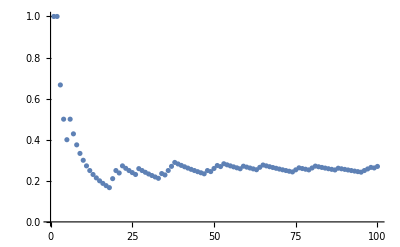

```mathematica
(* d) *)
prvihK[vzorec__,k_]:=Take[vzorec,k]
rf = Table[First[relFrekvence[prvihK[vz,k],{1}]], {k,1,n}]
ListPlot[rf,PlotRange->{0,1}]
```

8. Zapišite prvih 10 decimalk števila √2 kot seznam cifer.

```mathematica
Clear["Global`*"]
x = Sqrt[2];
dcx = Floor[x*10^10]  (* generiramo celo število, ki predstavlja prvih 10 decimalk števila x. Potenco določimo glede na celi del *)
cifre[st_]:=IntegerDigits[st] (* celoštevislke cifre števila *)
cifre[dcx]
```

14142135623

{1,4,1,4,2,1,3,5,6,2,3}

9. Podatki so prvih 99 decimalk števila pi. Poskus je slučajna izbira elementa iz podatkov. 
	a) Pripravite podatke v obliki seznama v Mathematici. 
	b) Generirajte 50 realizacij poskusa slučajne izbire števke iz množice podatkov. 
	c) Izračunajte relativno frekvenco števke 9. 
	d) Izračunajte verjetnost, da je števka večja od 7.
Rezultati: a) -, b) -, c) P(x=9)=13/100, d) P(x>7)=1/4.

```mathematica
Clear["Global`*"]
(* a) *)
podatki = IntegerDigits[Floor[Pi*10^99]]

(* b) *)
 vzorec = Table[RandomChoice[podatki],{50}]

(* c) *)
(* Teoretična verjetnost za 9 *)
Count[podatki, 9]/Length[podatki]
(* relativna frekvenca za 9 *)
Count[vzorec, 9]/Length[vzorec]

(* d) *)
(Count[podatki, 8]+ Count[podatki, 9])/Length[podatki]
Sum[Count[podatki, i], {i, 8,9}]/Length[podatki]
1-Sum[Count[podatki, i], {i, 0,7}]/Length[podatki]
```

{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,7}

{5,0,9,6,5,9,0,6,3,8,9,4,9,2,9,3,9,2,5,7,0,2,3,0,8,2,9,9,6,9,5,1,6,8,4,1,9,6,2,9,9,7,1,3,1,9,4,1,5,4}

13/100

13/50

1/4

1/4

10. Vzorčni prostor je prvih 100 naravnih števil.
	a) Zapišite dogodka D7 in D3, da je število deljivo s 7 in da je deljivo s 3. 
	b) Zapišite dogodke D7 U D3, D7 D3, komplement D7. (Poiščite ustrezne ukaze v Mathematici.)

```mathematica
Clear["Global`*"]
(* a) *)
podatki = Range[100]
D7 = Select[podatki,Mod[#,7]==0&]
D3 = Select[podatki,Mod[#,3]==0&]
(* b) *)
(* D7 U D3 *)
Union[D7, D3]
(* D7 presek D3 *)
Intersection[D7, D3]
(* D7 komplement *)
Complement[podatki, D7]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

{7,14,21,28,35,42,49,56,63,70,77,84,91,98}

{3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54,57,60,63,66,69,72,75,78,81,84,87,90,93,96,99}

{3,6,7,9,12,14,15,18,21,24,27,28,30,33,35,36,39,42,45,48,49,51,54,56,57,60,63,66,69,70,72,75,77,78,81,84,87,90,91,93,96,98,99}

{21,42,63,84}

{1,2,3,4,5,6,8,9,10,11,12,13,15,16,17,18,19,20,22,23,24,25,26,27,29,30,31,32,33,34,36,37,38,39,40,41,43,44,45,46,47,48,50,51,52,53,54,55,57,58,59,60,61,62,64,65,66,67,68,69,71,72,73,74,75,76,78,79,80,81,82,83,85,86,87,88,89,90,92,93,94,95,96,97,99,100}

11. Obravnavamo komplet igralnih kart z vrednostmi 2-as in barvami, karo, srce, križ, pik. Poskus je izbira dveh kart. 
	a) Pripravite seznam kart v obliki seznama.
	b) Generirajte vzorec 100 izborov dveh kart. 
Obravnavamo dogodka A:‘karti imata enako barvo’ in B:‘obe karti imata vrednost 10 ali več’. Za naslednje dogodke izračunajte relativno frekvenco in verjetnost. 
	c) A, B, AB, komplement B, AUB
Rezultati: a) -, b) -, c) P(A)=4/17, P(B)=95/663, P(AB)=20/663, P(B^C)=568/663, P(AUB)=77/221.

```mathematica
Clear["Global`*"]
(* a) *)
barva={"srce","karo","pik","kriz"}
vrednost=Join[CharacterRange["2","9"],{"10","fant","dama","kralj","as"}]
Needs["Combinatorica`"] (* Knjižnica v katerem je ukaz CartesianProduct *)
karte=CartesianProduct[vrednost,barva]
```

{srce,karo,pik,kriz}

{2,3,4,5,6,7,8,9,10,fant,dama,kralj,as}

{{2,srce},{2,karo},{2,pik},{2,kriz},{3,srce},{3,karo},{3,pik},{3,kriz},{4,srce},{4,karo},{4,pik},{4,kriz},{5,srce},{5,karo},{5,pik},{5,kriz},{6,srce},{6,karo},{6,pik},{6,kriz},{7,srce},{7,karo},{7,pik},{7,kriz},{8,srce},{8,karo},{8,pik},{8,kriz},{9,srce},{9,karo},{9,pik},{9,kriz},{10,srce},{10,karo},{10,pik},{10,kriz},{fant,srce},{fant,karo},{fant,pik},{fant,kriz},{dama,srce},{dama,karo},{dama,pik},{dama,kriz},{kralj,srce},{kralj,karo},{kralj,pik},{kralj,kriz},{as,srce},{as,karo},{as,pik},{as,kriz}}

```mathematica
(* b) *)
RandomChoice[karte,2] (* izbor dveh kart iz seznama karte *)
RandomSample[karte,2] (* izbor dveh kart iz seznama karte *)
vzorec=Table[RandomSample[karte,2],{i,1,100}];

(* c) *)
A = Select[vzorec, #[[1,2]] == #[[2, 2]]&];
(* rel frekvenca *)
Length[A]/Length[vzorec] //N
(* P(A) *)
PA = 4*Binomial[13, 2]/ Binomial[52, 2] //N

visoke = {"10", "fant", "dama", "kralj", "as"};
B = Select[vzorec, MemberQ[visoke, #[[1,1]]] && MemberQ[visoke, #[[2,1]]]&];
Length[B] / Length[vzorec] //N
PB = Binomial[20, 2]/Binomial[52, 2] //N

(* Presek *)
Length[Intersection[A,B]]/Length[vzorec] //N
PAB =4*Binomial[5, 2]/Binomial[52,2] //N

(* Unija *)
Length[Intersection[A,B]]/Length[vzorec] //N
PAUB = PA+PB-PAB //N

(* Komplement *)
Length[Complement[vzorec, B]]/Length[vzorec] //N
1-PB //N
```

{{4,kriz},{dama,srce}}

{{as,pik},{3,kriz}}

0.2

0.235294

0.11

0.143288

0.03

0.0301659

0.03

0.348416

0.86

0.856712

12. Igralec se poteguje za nagrado. Igra poteka na naslednji način. V prvem krogu meče dva kovanca, pri čemer se beleži število dobljenih cifer. Nato v drugem krogu meče igralno kocko, in sicer ima na voljo toliko metov, kolikor cifer je dosegel v prvem krogu. Nagrado dobi, če v drugem krogu doseže na kocki vsaj enkrat šest pik. 
	a) Z računalnikom simulirajte 100 krogov te igre. 
	b) Kolikšna je verjetnost, da bo igralec dobil nagrado?
	c) Denimo, da je igralec dobil nagrado. Kolikšna je tedaj verjetnost, da je v prvem krogu dosegel 0, 1 oziroma 2 cifri?
Rezultati: a) -, b) P(A)=23/144, c) P(H_1|A)=0, P(H_2|A)=12/23, P(H_3|A)=11/23.

```mathematica
(* a) *)
prvi:=Count[Table[RandomChoice[{"C","G"}],{i,1,2}],"C"];
drugi:=Table[RandomChoice[Range[6]],{i,1,prvi}];
igre=Table[If[Max[drugi]==6,True,False],{i,1,100}];
Count[igre,True]

(* b) *)
(* Popolna verjetnost *)
PA = 0*1/4+1/6*1/2+11/36*1/4

(* c) *)
(* Bayesov obrazec *)
PH1A = (0*1/4)/PA
PH2A = (1/6*1/2)/PA
PH3A =(11/36*1/4)/PA
PH1A + PH2A +PH3A
```

18

23/144

0

12/23

11/23

1

13. Sočasno vržemo dve igralni kocki. Kolikšne so verjetnosti dogodkov: 
	a) Vsaj na eni kocki pade število pik, ki je deljivo s 3. 
	b) Vsota pik je deljiva s 3, ob pogoju, da je vsota pik deljiva z 2.
	c) Vsota pik je vsaj 9, če vemo, da je vsota pik več kot 6.
	d) Razlika pik je 2, če vemo, da je vsota pik večja od 8.
Rezultati: a) 5/9, b) 1/3, c) 10/21, d) 1/5.

```mathematica
Clear["Global`*"]
(* Pogojne verjetnosti *)
(* a) *)
p1 = 20/36

(* b) *)
(* P(A|B) = P(A B)/P(B) *)
(* hkrati deljivo z 2 in 3 oziroma 6*)
p2 = (6/36)/(18/36)

(* c) *)
p3 = (10/36)/(21/36)

(* d) *)
p4 = (2/36)/(10/36)
```

5/9

1/3

10/21

1/5

14. Trije strelci sočasno ustrelijo v tarčo z verjetnostjo zadetkov 0.2, 0.4 in 0.6. Kolikšne so verjetnosti dogodkov: 
	a) Tarča ni zadeta. 
	b) Tarča je zadeta natanko enkrat.
	c) Tarča je zadeta vsaj enkrat.
	d) Tarčo je zgrešil tretji strelec, če smo videli, da sta v tarči dva zadetka.
Rezultati: a) 0.192, b) 0.464, c) 0.808, d) 0.108108.

```mathematica
p1=0.2;p2=0.4;p3=0.6;
pA = (1-p1)(1-p2)(1-p3)
pB = p1(1-p2)(1-p3)+(1-p1)p2(1-p3)+(1-p1)(1-p2)p3
pC = 1-pA
(* v tarči sta dva zadetka *)
p1 p2 (1-p3)+p1(1-p2)p3+(1-p1)p2 p3
(* Bayesov obrazec -- P(A|Hi)*P(Hi) = P(Hi|A)*P(A) ; računamo P(Hi|A)  *)
pD = p1 p2(1-p3)/ (p1 p2(1-p3)+p1(1-p2)p3+(1-p1)p2 p3)
(* v tarči so trije zadetki *)
p1 p2 p3
```

0.192

0.464

0.808

0.108108

15. Imamo 4 posode: v prvi je 5 belih in 5 črnih kroglic, v drugi je 1 bela in 2 črni kroglici, v tretji sta 2 beli in 5 črnih kroglic, v četrti pa so 3 bele in 7 črnih kroglic. Na slepo sežemo v eno izmed posod in iz nje izvlečemo kroglico.
	a) Kolikšna je verjetnost dogodka, da je izvlečena kroglica črna? 
	b) Kolikšna je verjetnost, da smo segli v četrto posodo, če smo izvlekli črno kroglico?
Rezultati: a) 271/420, b) 147/542.

```mathematica
Clear["Global`*"]
(* a) *)
P1 = (5/10)*(1/4)+(2/3)*(1/4)+(5/7)*(1/4)+(7/10)*(1/4)

(* b) *)
(* Bayesov obrazec: P(H4|A) = P(A|H4)*P(H4)/P(A) *)
PH4A = (7/10)*(1/4)/P1
```

271/420

147/542

16. Izpit z vprašanji izbirnega tipa vsebuje 25 vprašanj, pri vsakem so dani 4 možni odgovori. Privzemimo, da študent na vsako vprašanje odgovarja z ugibanjem. 
	a) Kolikšna je verjetnost, da študent pravilno odgovori na vsaj 20 vprašanj? 
	b) Kolikšna je verjetnost, da študent pravilno odgovori na manj kot 5 vprašanj?
	c) Poiščite pričakovano vrednost za število pravilno odgovorjenih vprašanj.
	d) Poiščite varianco za število pravilno odgovorjenih vprašanj.
	e) Poiščite standardni odklon od pričakovane vrednosti za število pravilno odgovorjenih vprašanj.
Rezultati: a) 1.24346×10^-8, b) 0.213741, c) 6.25, d) 4.6875, e) 2.16506.

```mathematica
(* Binomska porazdelitev: P(X = k) = ({{n}, {k}}) p^k (1-p)^(n-k) *)
p=; n=;
(* c) *)
(* E(X) = n p *)
(* d) *)
(* Var(X) = n p (1-p) *)
(* e) *)
(* Std(X) = √(Var(X)) *)
```

17. Dana je slučajna spremenljivka X z verjetnostno shemo X: (2 | 3 | 5 | 8
0.2 | 0.4 | 0.3 | 0.1). Določite naslednje vrednosti:
	a) P(X <= 3), 
	b) P(X > 2.5),
	c) P(2.7 < X < 5.1),
	d) E(X),
	e) Var(X).
Rezultati: a) 0.6, b) 0.8, c) 0.7, d) 3.9, e) 3.09.

```mathematica
(* d) *)
(* E(X) = ∑_i Subscript[x, i] Subscript[p, i] *)
(* e) *)
(* Var(X) = E(X^2) - E(X)^2 = ∑_i Subscript[x, i]^2 Subscript[p, i] - (∑_i Subscript[x, i] Subscript[p, i])^2 *)
```